```mathematica
UG=Import["C:\\fpgithub\\0908-LHWZ\\data\\02_Uran_Untergrund_1000-4000-100.txt","Table","NumberPoint"->","];
U=Import["C:\\fpgithub\\0908-LHWZ\\data\\01_Uran_Zaehlrohrcharakteristik_1000-4000-100.txt","Table","NumberPoint"->","];Smgr=Import["C:\\fpgithub\\0908-LHWZ\\data\\07_Sm_ggrFl_Zaehlrohrcharakteristik_1000-2200-100.txt","Table","NumberPoint"->","];
K=Import["C:\\fpgithub\\0908-LHWZ\\data\\10_K_m9_Zaehlrohrcharakteristik_2500-4000-100.txt","Table","NumberPoint"->","];
```

```mathematica
UG;
U;
Ub=Table[{U[[i,1]],U[[i,2]]-UG[[i,2]]},{i,1,Length[U]}];
Smgr
Smgrb=Table[{Smgr[[i,1]],Smgr[[i,2]]-UG[[i,2]]},{i,1,Length[Smgr]}]
K
Kb=Table[{K[[i,1]],K[[i,2]]-UG[[i+15,2]]},{i,1,Length[K]}]
```

{{1000.,0.32},{1100.,0.72},{1200.,0.48},{1300.,0.6},{1400.,0.58},{1500.,0.76},{1600.,0.86},{1700.,0.72},{1800.,0.8},{1900.,0.8},{2000.,0.94},{2100.,1.08},{2200.,0.9}}

{{1000.,0.32},{1100.,0.7},{1200.,0.34},{1300.,0.58},{1400.,0.58},{1500.,0.76},{1600.,0.86},{1700.,0.72},{1800.,0.76},{1900.,0.76},{2000.,0.94},{2100.,1.},{2200.,0.8}}

{{2500.,11.86},{2600.,10.3},{2700.,4.84},{2800.,4.82},{2900.,5.54},{3000.,5.86},{3100.,6.6},{3200.,6.34},{3300.,6.26},{3400.,8.54},{3500.,8.28},{3600.,11.9},{3700.,14.02},{3800.,17.92},{3900.,23.26},{4000.,30.8}}

{{2500.,11.66},{2600.,10.},{2700.,4.32},{2800.,4.28},{2900.,5.1},{3000.,5.26},{3100.,5.76},{3200.,5.58},{3300.,5.52},{3400.,7.82},{3500.,7.06},{3600.,11.02},{3700.,10.54},{3800.,14.88},{3900.,14.74},{4000.,24.38}}

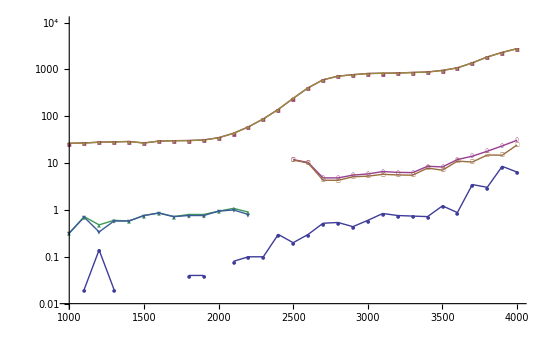

```mathematica
ListLogPlot[{UG,U,Ub,Smgr,Smgrb,K,Kb},PlotRange->{0.01,10^4},Joined->True,PlotMarkers->{Automatic,5}]
```

{1,1.7,2.88}

{π,9.0792,26.0576}

{0.235,0.386,0.774}

0.096

{0.139,0.29,0.678}

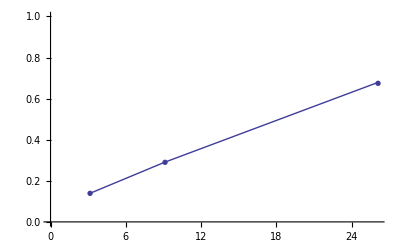

```mathematica
r={1,1.7,2.88}
F=r^2 π
Sm={0.235,0.386,0.774}
Unt=0.096
Sm-Unt
ListPlot[Table[{F[[i]],(Sm-Unt)[[i]]},{i,1,3}],PlotRange->{0,1},Joined->True,PlotMarkers->{Automatic,7}]
```

```mathematica
1/(0.16*0.045^2)
```

3086.42